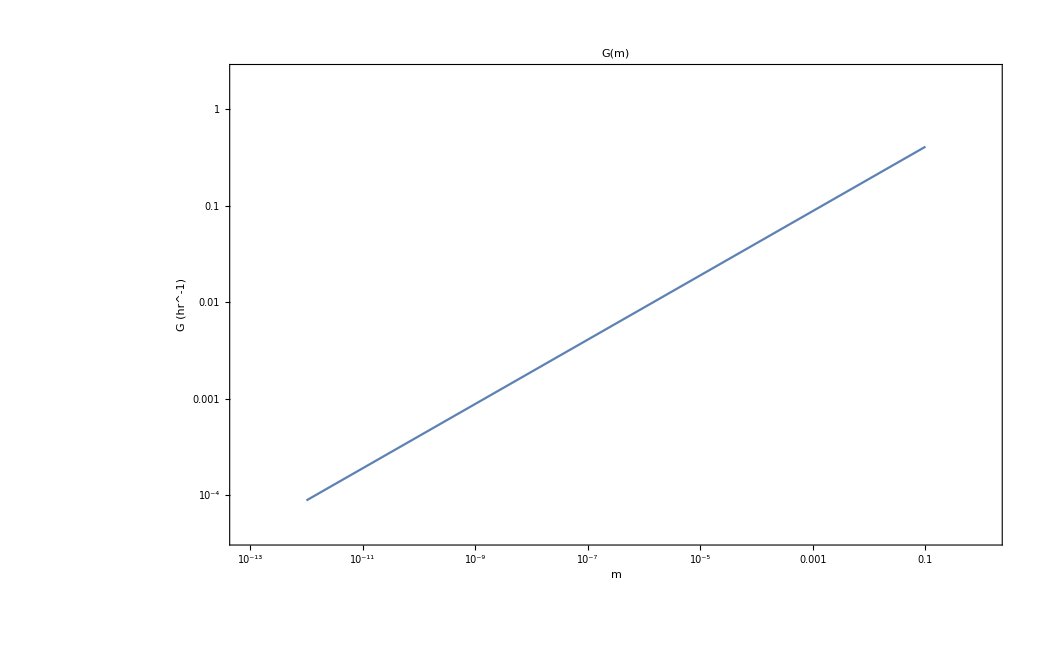

```mathematica
LogLogPlot[{(0.68 m)^(1/3)}, {m,10^-12,10^-1},Frame->{True,True,False,False},FrameLabel->{"m","G (hr^-1)"},PlotLabel->"G(m)", LabelStyle->Directive[Bold],BaseStyle->FontSize->24]
```

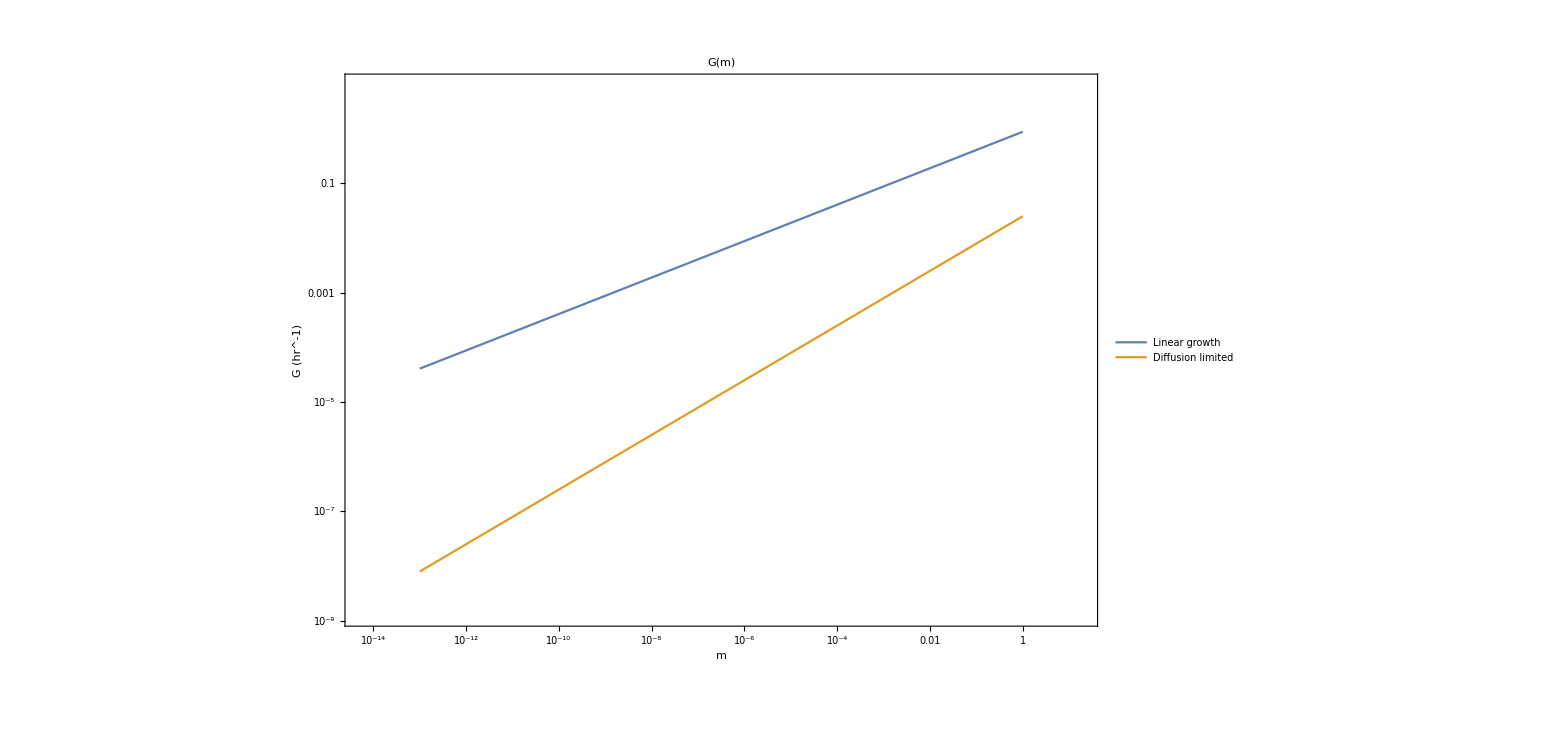

```mathematica
LogLogPlot[{(0.68p)^(1/3),( 6.3 10^-4 p)^(1/2)},{p,10^-13,1},PlotLegends->Placed[LineLegend[{"Linear growth","Diffusion limited"},Joined->Automatic,LegendFunction->Frame,LegendMarkerSize->{{20,10}}],{{0.75,0.1},{0.2,0.02}}], Frame->{True,True,False,False},FrameLabel->{"m","G (hr^-1)"},PlotLabel->"G(m)", LabelStyle->Directive[Bold],BaseStyle->FontSize->24]
```

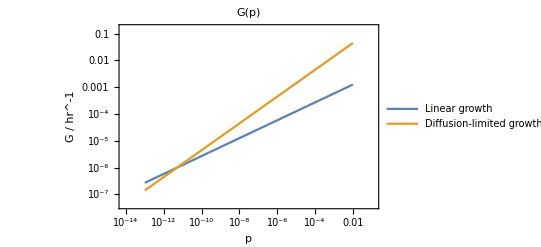

```mathematica
{"Linear growth", "Diffusion-limited growth"},PlotLegends->Position-> [0.1,0.1]
```

```mathematica
Directory[]
```

/phys/linux/s1338295/Code/*crine

```mathematica
SetDirectory["/phys/linux/s1338295/Data/lattice"]
```

/phys/linux/s1338295/Data/lattice

```mathematica
d0dat=ReadList["B_d=0_N=1e9.dat",Record,3]
```

{0   0   0,1e-7    2.8171e-3   0.0664e-3,1e-6    7.0890e-3    0.3049e-3}

```mathematica
dat1=Import["B_d=0_N=1e9.dat","FieldSeparators"-> ","]//Grid
```

0 | 0 | 0
1.×10^-7 | 0.0028171 | 0.0000664
1.×10^-6 | 0.007089 | 0.0003049

```mathematica
ListPlot[dat1]
```

ListPlot::lpn: 0. | 0. | 0.
1.×10^-7 | 0.0028171 | 0.0000664
1.×10^-6 | 0.007089 | 0.0003049 is not a list of numbers or pairs of numbers.

ListPlot[0 | 0 | 0
1.×10^-7 | 0.0028171 | 0.0000664
1.×10^-6 | 0.007089 | 0.0003049]

```mathematica
Take[dat1[[1,2]]]
```

{1.×10^-7,0.0028171,0.0000664}

```mathematica
dat1=Import["gr1.dat","FieldSeparators"-> ","]
```

{{0,0},{1.×10^-7,0.0028171},{1.×10^-6,0.007089}}

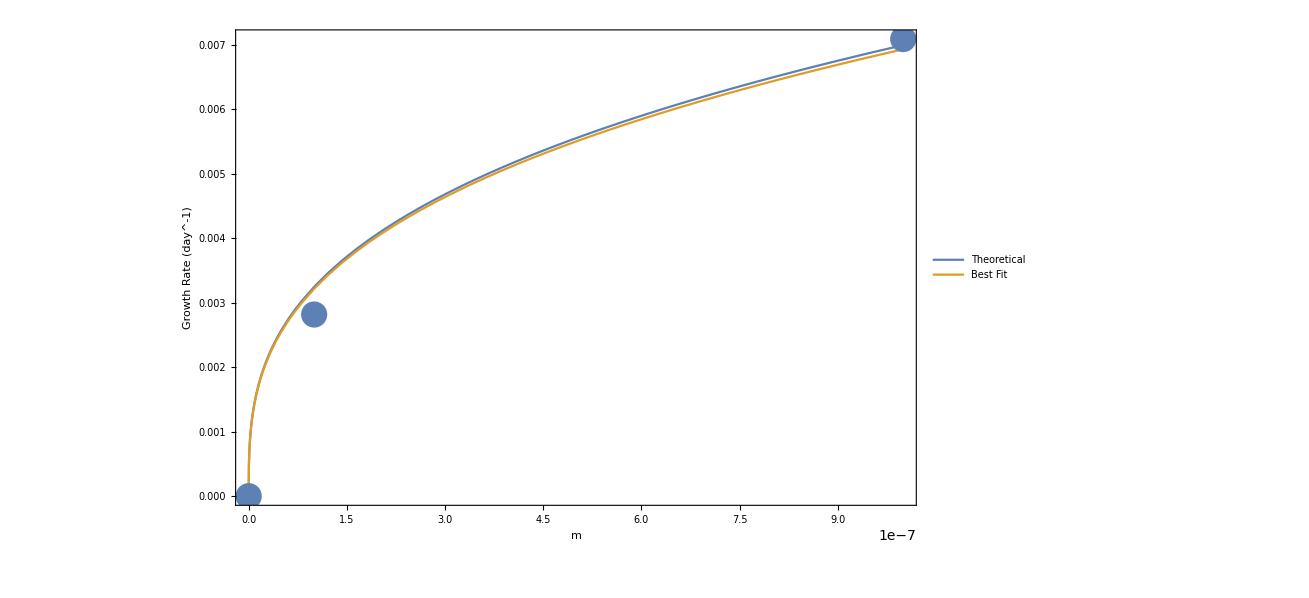

```mathematica
Show[Plot[{0.6994  x^(1/3),0.693 x^(1/3)},{x,0,10^-6},PlotLegends->Placed[LineLegend[{"Theoretical","Best Fit"},Joined->Automatic,LegendFunction->Frame,LegendMarkerSize->{{20,10}}],{{0.75,0.1},{0.2,0.02}}], Frame->{True,True,False,False},FrameLabel->{"m","Growth Rate (day^-1)"}],ListPlot[dat1],PlotRange->{{0,10^-6},All},PlotLabel->None,LabelStyle->{GrayLevel[0]},BaseStyle->FontSize->22]
```

```mathematica
dat2=Import["gr2.dat","FieldSeparators"-> ","]
```

{{0,0},{1.×10^-6,0.03168},{0.00001,0.05043},{0.0001,0.08355}}

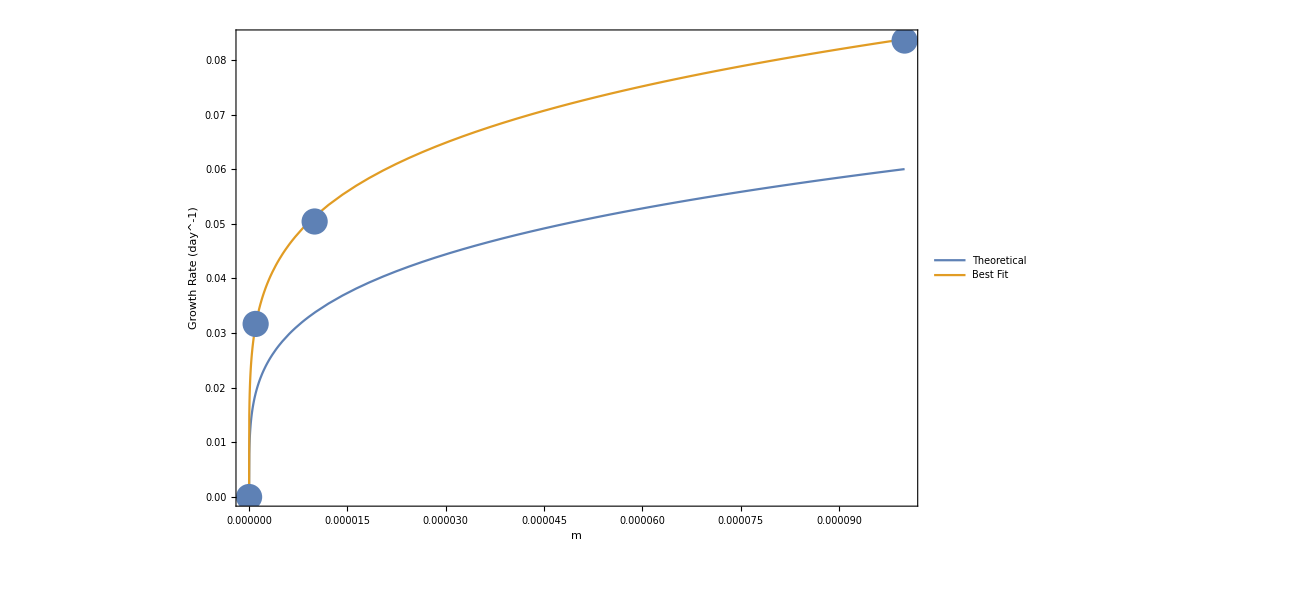

```mathematica
Show[Plot[{0.6002  x^(1/4),0.5961x^(0.213)},{x,0,10^-4},PlotLegends->Placed[LineLegend[{"Theoretical","Best Fit"},Joined->Automatic,LegendFunction->Frame,LegendMarkerSize->{{20,10}}],{{0.75,0.1},{0.2,0.02}}], Frame->{True,True,False,False},FrameLabel->{"m","Growth Rate (day^-1)"}],ListPlot[dat2],PlotRange->{{0,10^-4},All},PlotLabel->None,LabelStyle->{GrayLevel[0]},BaseStyle->FontSize->22]
```

```mathematica
ListPlot[dat2]
```

-Graphics-